## Calculation of the Efficiency of DQC Pulse Sequences for Several Finite Square Pulses

Load the packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<UsefulFunctions.m
```

Useful functions loaded. Run the command, uf$list[] to get a list of functions

```mathematica
<<OpQ.m
<<Multiplication.m
<<Commutator.m
<<Evolve.m
<< TenSH.m
```

Loaded ScalarQ(), OperatorQ(), SimpleOperatorQ(),
CreateScalar(), CreateOperator()

Loaded Mult(), NCSort(), SortedMult(), MultSort()

Loaded Comm()

Loaded Evolve()

Loaded Ixe1, Iye1, Ize1

Loaded Ixe2, Iye2, Ize2

Loaded Ixe3, Iye3, Ize3

Loaded Ixe4, Iye4, Ize4

Loaded Ixe5, Iye5, Ize5

Loaded Ixe6, Iye6, Ize6

Loaded Ixe7, Iye7, Ize7

Loaded Ixe8, Iye8, Ize8

Loaded Ixe9, Iye9, Ize9

Loaded Ixe10, Iye10, Ize10

```mathematica
(* Define Free Evolution *)
FreeEvolution[t_,C1_,C2_,a12_,op_]:=Evolve[Mult[Ize1,Ize2],a12*t,Evolve[Ize2,C2*t,Evolve[Ize1,C1*t,op]]]/.Mult->SortedMult;
(* Define Modified Propagator for Finite Pulses *)
fp[C1_,C2_,B1_,t_,op_,dir_]:=Module[{A1,A2,A3},
A1 = Evolve[Iye2*Cos[dir]-Ixe2*Sin[dir],ArcTan[C2/B1],Evolve[Iye1*Cos[dir]-Ixe1*Sin[dir],ArcTan[C1/B1],op]]/.Mult->SortedMult;
A2 = Evolve[Ixe2*Cos[dir] + Iye2*Sin[dir],√(B1^2+C2^2)*t,Evolve[Ixe1*Cos[dir] + Iye1*Sin[dir],√(B1^2+C1^2)*t,A1]]/.Mult->SortedMult;
A3 = Evolve[Iye2*Cos[dir]-Ixe2*Sin[dir],-ArcTan[C2/B1],Evolve[Iye1*Cos[dir]-Ixe1*Sin[dir],-ArcTan[C1/B1],A2]]/.Mult->SortedMult;
Return[A3];
];
```

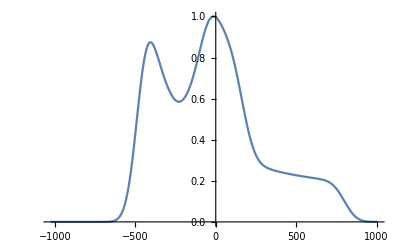

```mathematica
(* Load Nitroxide ESR Speactrum *)
lineshape = Import["nitroxide_spectrum.txt", "Data"];
lineshape[[All,2]] = lineshape[[All,2]] / Max[lineshape[[All,2]]];
lineshape[[All,1]] = (lineshape[[All,1]] -16975);
f = ListInterpolation[lineshape[[All,2]],2*π*lineshape[[All,1]]];
Plot[f[x],{x,2*π*Min[lineshape[[All,1]]],2*π*Max[lineshape[[All,1]]]}]
```

```mathematica
(* Calculate the Finite Pulse Efficiencies for a Single Datapoint in a DQC Time-Domain Signal *)
tm = 2.0;tp1 = 0.5;t21 = tm-tp1;a12=2*π*1.9;t1=0.02;
cmin = -650.;cmax = 900.;
nsize = 80;
cvals = Flatten[Table[{c1,c2},{c1,cmin,cmax,(cmax-cmin)/(nsize-1)},{c2,cmin,cmax,(cmax-cmin)/(nsize-1)}],1];
dim=Dimensions[cvals][[1]];
normf = Total[f[cvals[[All,1]]]*f[cvals[[All,2]]]];
```

### Hard pulses

```mathematica
tau = 1.*10^-8; (* in μs; π-pulse duration = 2*tau *)
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

10.967

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

-1.03125×10^-9 Iye1+0.951057 Ize1-9.0933×10^-8 Mult[Ixe1,Ixe2]-0.618034 Mult[Ixe1,Iye2]-3.26669×10^-10 Mult[Ixe1,Ize2]+9.0933×10^-8 Mult[Iye1,Iye2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

122.516

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

1.36692×10^-7 Ixe1-5.32749×10^-9 Ixe2+3.80278×10^-7 Iye1-0.951057 Ize1-9.0933×10^-8 Mult[Ixe1,Ixe2]+0.618034 Mult[Ixe1,Iye2]+1.49461×10^-7 Mult[Ixe1,Ize2]+9.0933×10^-8 Mult[Iye1,Iye2]+3.27926×10^-8 Mult[Iye1,Ize2]+8.88278×10^-8 Mult[Ize1,Iye2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

10.0615

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

9.0748×10^-8 Mult[Ixe1,Ixe2]+0.618034 Mult[Ixe1,Ize2]-9.0748×10^-8 Mult[Iye1,Ize2]-9.0748×10^-8 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

71.411

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

0.25 Iye1-7.19686×10^-10 Mult[Ixe1,Ixe2]-0.363271 Mult[Ixe1,Ize2]+7.19686×10^-10 Mult[Ize1,Ize2]

### 2ns / 4ns-pulses

```mathematica
tau = 2.*10^-3;
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

12.4251

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

0.00368009 Ixe1+0.0292524 Iye1+0.815715 Ize1-0.0223186 Mult[Ixe1,Ixe2]-0.396198 Mult[Ixe1,Iye2]+0.0114844 Mult[Ixe1,Ize2]+0.00125965 Mult[Iye1,Ixe2]+0.0222827 Mult[Iye1,Iye2]-0.000643612 Mult[Iye1,Ize2]+1.58974×10^-6 Mult[Ize1,Ixe2]-0.0000175786 Mult[Ize1,Iye2]+1.84182×10^-6 Mult[Ize1,Ize2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

174.646

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

-0.000382859 Ixe1-0.00057512 Ixe2-0.00523232 Iye1-0.0000361671 Iye2-0.627084 Ize1+7.71791×10^-8 Ize2-0.0181224 Mult[Ixe1,Ixe2]+0.320127 Mult[Ixe1,Iye2]+0.00402142 Mult[Ixe1,Ize2]-0.00119374 Mult[Iye1,Ixe2]+0.0179844 Mult[Iye1,Iye2]+0.00323809 Mult[Iye1,Ize2]-0.000603388 Mult[Ize1,Ixe2]+0.00960148 Mult[Ize1,Iye2]+0.00128426 Mult[Ize1,Ize2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

10.0473

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

0.0157577 Mult[Ixe1,Ixe2]-0.0201085 Mult[Ixe1,Iye2]+0.278241 Mult[Ixe1,Ize2]-0.00091686 Mult[Iye1,Ixe2]+0.00116416 Mult[Iye1,Iye2]-0.0162621 Mult[Iye1,Ize2]-0.000952904 Mult[Ize1,Ixe2]+0.00120623 Mult[Ize1,Iye2]-0.0169236 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

71.6207

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

-7.92564×10^-6 Ixe1+4.16048×10^-6 Ixe2+0.0964278 Iye1-1.76623×10^-6 Iye2-0.000507025 Ize1+0.00117588 Mult[Ixe1,Ixe2]+0.00257348 Mult[Ixe1,Iye2]-0.120329 Mult[Ixe1,Ize2]-4.19847×10^-6 Mult[Iye1,Ixe2]-9.25169×10^-6 Mult[Iye1,Iye2]+0.000332379 Mult[Iye1,Ize2]+6.93283×10^-6 Mult[Ize1,Ixe2]+0.0000163308 Mult[Ize1,Iye2]-0.000309303 Mult[Ize1,Ize2]

### 3ns / 6ns-pulses

```mathematica
tau = 3.*10^-3;
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

12.7095

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

0.0205769 Ixe1+0.0237988 Iye1+0.704715 Ize1-0.0249262 Mult[Ixe1,Ixe2]-0.26624 Mult[Ixe1,Iye2]+0.0127137 Mult[Ixe1,Ize2]+0.00233392 Mult[Iye1,Ixe2]+0.0248952 Mult[Iye1,Iye2]-0.00118266 Mult[Iye1,Ize2]+1.79985×10^-6 Mult[Ize1,Ixe2]-0.000116987 Mult[Ize1,Iye2]+0.000030397 Mult[Ize1,Ize2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

175.913

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

-0.0320916 Ixe1-0.000218542 Ixe2-0.0257859 Iye1-0.0000167017 Iye2-0.455509 Ize1+6.3412×10^-7 Ize2-0.0130801 Mult[Ixe1,Ixe2]+0.198713 Mult[Ixe1,Iye2]+0.00755212 Mult[Ixe1,Ize2]-0.000760852 Mult[Iye1,Ixe2]+0.0111887 Mult[Iye1,Iye2]-0.00308991 Mult[Iye1,Ize2]-0.000293335 Mult[Ize1,Ixe2]+0.00370708 Mult[Ize1,Iye2]+0.00154093 Mult[Ize1,Ize2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

9.8999

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

0.00919425 Mult[Ixe1,Ixe2]-0.0153922 Mult[Ixe1,Iye2]+0.16474 Mult[Ixe1,Ize2]-0.00065777 Mult[Iye1,Ixe2]+0.00109522 Mult[Iye1,Iye2]-0.00991751 Mult[Iye1,Ize2]-0.000767592 Mult[Ize1,Ixe2]+0.0012795 Mult[Ize1,Iye2]-0.0113831 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

71.7494

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

-0.0000171187 Ixe1+0.0000148956 Ixe2+0.0554662 Iye1+2.34178×10^-6 Iye2-0.000499953 Ize1-0.000716297 Mult[Ixe1,Ixe2]+0.00458916 Mult[Ixe1,Iye2]-0.0658746 Mult[Ixe1,Ize2]+4.59307×10^-6 Mult[Iye1,Ixe2]-0.0000325666 Mult[Iye1,Iye2]+0.000532359 Mult[Iye1,Ize2]-9.19202×10^-6 Mult[Ize1,Ixe2]+0.0000584687 Mult[Ize1,Iye2]-0.00109903 Mult[Ize1,Ize2]

### 4ns / 8ns-pulses

```mathematica
tau = 4.*10^-3;
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

12.9098

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

0.0251905 Ixe1+0.0142314 Iye1+0.619957 Ize1-0.0175403 Mult[Ixe1,Ixe2]-0.182184 Mult[Ixe1,Iye2]+0.0107166 Mult[Ixe1,Ize2]+0.00170244 Mult[Iye1,Ixe2]+0.0176118 Mult[Iye1,Iye2]-0.00106989 Mult[Iye1,Ize2]-0.0000186529 Mult[Ize1,Ixe2]-0.0000984194 Mult[Ize1,Iye2]+0.0000515056 Mult[Ize1,Ize2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

174.428

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

-0.0450336 Ixe1+0.0000128381 Ixe2-0.0435005 Iye1+2.16409×10^-6 Iye2-0.342447 Ize1+4.79834×10^-7 Ize2-0.00696916 Mult[Ixe1,Ixe2]+0.134223 Mult[Ixe1,Iye2]+0.0146682 Mult[Ixe1,Ize2]-0.0000394402 Mult[Iye1,Ixe2]+0.00421008 Mult[Iye1,Iye2]-0.0095866 Mult[Iye1,Ize2]+0.0000203384 Mult[Ize1,Ixe2]-0.000168371 Mult[Ize1,Iye2]+0.000422986 Mult[Ize1,Ize2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

10.167

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

0.00402993 Mult[Ixe1,Ixe2]-0.0108381 Mult[Ixe1,Iye2]+0.108755 Mult[Ixe1,Ize2]-0.000472823 Mult[Iye1,Ixe2]+0.000857606 Mult[Iye1,Iye2]-0.005017 Mult[Iye1,Ize2]-0.000745602 Mult[Ize1,Ixe2]+0.00129293 Mult[Ize1,Iye2]-0.00675483 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

71.2713

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

5.45217×10^-6 Ixe1+0.0000137093 Ixe2+0.0364294 Iye1+0.0000132946 Iye2-0.000367489 Ize1-0.00290652 Mult[Ixe1,Ixe2]+0.00299886 Mult[Ixe1,Iye2]-0.0428923 Mult[Ixe1,Ize2]-0.0000611342 Mult[Iye1,Ixe2]+0.0000625489 Mult[Iye1,Iye2]-0.000577449 Mult[Iye1,Ize2]-0.0000521841 Mult[Ize1,Ixe2]+0.0000538121 Mult[Ize1,Iye2]-0.000830139 Mult[Ize1,Ize2]

### 5ns / 10ns-pulses

```mathematica
tau = 5.*10^-3;
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

12.7495

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

0.00133687 Ixe1+0.0130946 Iye1+0.570951 Ize1-0.00898012 Mult[Ixe1,Ixe2]-0.131529 Mult[Ixe1,Iye2]+0.00882668 Mult[Ixe1,Ize2]+0.000645162 Mult[Iye1,Ixe2]+0.00903659 Mult[Iye1,Iye2]-0.000662256 Mult[Iye1,Ize2]-6.0924×10^-6 Mult[Ize1,Ixe2]-0.000011657 Mult[Ize1,Iye2]+0.0000112713 Mult[Ize1,Ize2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

175.128

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

-0.033588 Ixe1+0.0000826476 Ixe2-0.0498961 Iye1+4.16455×10^-6 Iye2-0.258207 Ize1+5.96948×10^-8 Ize2-0.00355887 Mult[Ixe1,Ixe2]+0.098042 Mult[Ixe1,Iye2]+0.020868 Mult[Ixe1,Ize2]+0.0000395416 Mult[Iye1,Ixe2]+0.00126167 Mult[Iye1,Iye2]-0.00942558 Mult[Iye1,Ize2]+0.0000679925 Mult[Ize1,Ixe2]-0.00137275 Mult[Ize1,Iye2]-0.000387945 Mult[Ize1,Ize2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

9.93879

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

0.00161791 Mult[Ixe1,Ixe2]-0.00792764 Mult[Ixe1,Iye2]+0.07766 Mult[Ixe1,Ize2]-0.000318034 Mult[Iye1,Ixe2]+0.000601763 Mult[Iye1,Iye2]-0.0025935 Mult[Iye1,Ize2]-0.000751691 Mult[Ize1,Ixe2]+0.00131408 Mult[Ize1,Iye2]-0.00462403 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

72.3286

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

-3.86051×10^-6 Ixe1+7.84114×10^-7 Ixe2+0.0259708 Iye1+4.60076×10^-6 Iye2-0.000152898 Ize1-0.00161637 Mult[Ixe1,Ixe2]+0.000246924 Mult[Ixe1,Iye2]-0.0313504 Mult[Ixe1,Ize2]-0.0000441197 Mult[Iye1,Ixe2]+7.34799×10^-6 Mult[Iye1,Iye2]-0.000513408 Mult[Iye1,Ize2]-0.000018059 Mult[Ize1,Ixe2]+3.07782×10^-6 Mult[Ize1,Iye2]-0.000372107 Mult[Ize1,Ize2]

### 8ns / 16ns-pulses

```mathematica
tau = 8.*10^-3;
ρ0 = Ize1;
ρ1A = fp[C1,C2,π/2/tau,tau,ρ0,0];
ρ2A = FreeEvolution[tp1,C1,C2,a12,ρ1A]/.Mult->SortedMult;
ρ3A = col$op[fp[C1,C2,π/(2*tau),(2*tau),ρ2A,0],2,1];
ρ4A := FreeEvolution[tp1,C1,C2,a12,ρ3A]/.Mult->SortedMult;
ρ5A[C1_,C2_] := Evaluate[fp[C1,C2,π/2/tau,tau,ρ4A,0]];
```

```mathematica
AbsoluteTiming[res0 = ParallelMap[Chop[Expand[ρ5A[#[[1]],#[[2]]]]]&,cvals];][[1]]
```

12.5304

```mathematica
ρ50 = Total[res0*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ50]
```

-0.0611553 Ixe1+0.0477006 Iye1+0.569787 Ize1-0.0020639 Mult[Ixe1,Ixe2]-0.0643225 Mult[Ixe1,Iye2]+0.00713519 Mult[Ixe1,Ize2]+0.0000577078 Mult[Iye1,Ixe2]+0.00204681 Mult[Iye1,Iye2]-0.00020826 Mult[Iye1,Ize2]+0.0000143795 Mult[Ize1,Ixe2]+6.31937×10^-6 Mult[Ize1,Iye2]-0.0000341326 Mult[Ize1,Ize2]

```mathematica
sub1 = {Mult[Ixe1,Iye2]->xy};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub3 = {xy->Mult[Ixe1,Iye2]};
res0A = Chop[res0/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res0[[j]]},{j,1,Dimensions[cvals][[1]]}];
res1 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res1[[j]]},{j,1,Dimensions[cvals][[1]]}];
res2 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res2[[j]]},{j,1,Dimensions[cvals][[1]]}];
res3 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t1,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

174.498

```mathematica
ρ80 = Total[res3*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ80]
```

-0.00651067 Ixe1+0.0000250674 Ixe2+0.0188065 Iye1+7.98623×10^-7 Iye2-0.0288922 Ize1-4.18067×10^-8 Ize2-0.000582348 Mult[Ixe1,Ixe2]+0.0479014 Mult[Ixe1,Iye2]+0.0116196 Mult[Ixe1,Ize2]+0.0000331074 Mult[Iye1,Ixe2]+0.000040942 Mult[Iye1,Iye2]-0.00278074 Mult[Iye1,Ize2]+0.0000141388 Mult[Ize1,Ixe2]-0.000423422 Mult[Ize1,Iye2]-0.000565872 Mult[Ize1,Ize2]

```mathematica
res3A = Chop[res3/.sub1/.sub2/.sub3];
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res3A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res4 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/2/tau,tau,#[[3]],0]]&,rho$vals];
][[1]]
```

9.94919

```mathematica
ρ90 = Total[res4*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ90]
```

0.0000515614 Mult[Ixe1,Ixe2]-0.00382323 Mult[Ixe1,Iye2]+0.0369027 Mult[Ixe1,Ize2]+0.000066315 Mult[Iye1,Ixe2]+0.000142379 Mult[Iye1,Iye2]-0.000448001 Mult[Iye1,Ize2]+0.000439443 Mult[Ize1,Ixe2]+0.000906226 Mult[Ize1,Iye2]-0.00175877 Mult[Ize1,Ize2]

```mathematica
sub4 = {Mult[Ixe1,Ize2]->xz};sub2 = {Ixe1->0,Iye1->0,Ize1->0,Ixe2->0,Iye2->0,Ize2->0};sub5 = {xz->Mult[Ixe1,Ize2]};
res4A = res4/.sub4/.sub2/.sub5;
```

```mathematica
AbsoluteTiming[
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res4A[[j]]},{j,1,Dimensions[cvals][[1]]}];
res5 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res5[[j]]},{j,1,Dimensions[cvals][[1]]}];
res6 = ParallelMap[Expand[fp[#[[1]],#[[2]],π/(2*tau),2*tau,#[[3]],0]]&,rho$vals];
rho$vals = Table[{cvals[[j,1]],cvals[[j,2]],res6[[j]]},{j,1,Dimensions[cvals][[1]]}];
res7 = ParallelMap[Expand[ReplaceAll[FreeEvolution[t21,#[[1]],#[[2]],a12,#[[3]]],Mult->SortedMult]]&,rho$vals];
][[1]]
```

71.069

```mathematica
ρ120 = Total[res7*f[cvals[[All,1]]]*f[cvals[[All,2]]]]/normf//Expand;
```

```mathematica
Chop[ρ120]
```

-0.00015914 Ixe1-6.08506×10^-6 Ixe2+0.0121917 Iye1-3.44697×10^-6 Iye2+0.0000289175 Ize1+0.000585462 Mult[Ixe1,Ixe2]-0.000687278 Mult[Ixe1,Iye2]-0.0140841 Mult[Ixe1,Ize2]+0.0000706498 Mult[Iye1,Ixe2]-0.000119253 Mult[Iye1,Iye2]-0.0000923655 Mult[Iye1,Ize2]+0.0000135301 Mult[Ize1,Ixe2]-0.0000238852 Mult[Ize1,Iye2]+0.000366004 Mult[Ize1,Ize2]